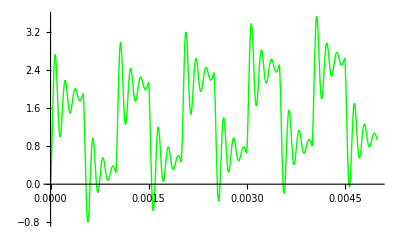

```mathematica
R1=3300;
R2=47000;
C1=39*10^-9;
C2=82 *10^-9; 
L=22 *10^-3; 

amplituda=5; 
frekvence=1000;

uZ[t]=amplituda*(1+Tanh[100 Sin[2*Pi*frekvence*t]])/2;

uzel1=iU[t]==iR1[t]+iL[t]+iR2[t];
uzel2=iR1[t]+iL[t]==iC1[t];
uzel3=iR2[t]+iC1[t]==iC2[t];

rez1=u1[t]-u2[t]==iR1[t]*R1;
rez2=u1[t]-u3[t]==iR2[t]*R2;
cond1=iC1[t]==C1*(u2'[t]-u3'[t]);
cond2=iC2[t]==C2*u3'[t];
ind=u1[t]-u2[t]==L*iL'[t];
zdroj=uZ[t]==u1[t];
podm1=u2[0]==0;
podm2=u3[0]==0;
podm3=iL[0]==0;

rovnice={uzel1,uzel2,uzel3,rez1,rez2,cond1,cond2,ind,zdroj,podm1,podm2,podm3};
nezname={iU[t],iR1[t],iR2[t],iC1[t],iC2[t],iL[t],u1[t],u2[t],u3[t]};
vysledek=NDSolve[rovnice,nezname,{t,0,5*1/frekvence},StartingStepSize->10^-10];

Plot[{u3[t]/.vysledek},{t,0,5*1/frekvence},PlotStyle->{{Green,Thick}}]
```